```mathematica
(* Start with the Quantum Rotor Hamiltonian in Eq 14: H = 1/2 *E^2 + h/2 *(2 -U - Udag) *)
```

```mathematica
(* Construct the flux matrix, a diagonal matrix of l^2 /2 values from -L to L, dimensionality 2L+1 *)
(* First make a table of the values *)
diagonalK[L_] := Table[(l^2)/2, {l, -L, L}]

(*diagonalK[2] // MatrixForm*)
(* This makes the matrix LzLz *)
LzLz[L_] := DiagonalMatrix[diagonalK[L]]
```

```mathematica
(*LzLz[2] //MatrixForm*)
```

```mathematica
(* Generating identity matrix of dimension 2L+1 *)
ident[L_] := IdentityMatrix[2L+1]
```

```mathematica
(* One link in the flux space has parameters h (gauge) and l (flux) and is described by Eq. 17: l^2 /2 delta(l',l) + h/2 (2delta(l',l) - delta(l'+1,l) - delta(l'-1,l)) *)

linkV[L_] := (2*ident[L] -  DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])
(*linkV[2] // MatrixForm*)
linkH[h_,L_]  := LzLz[L]+ (h/2)(2 ident[L] - DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])
(* linkH[2, 2] //MatrixForm
DiagonalMatrix[Table[1,4],1] // MatrixForm
DiagonalMatrix[Table[1,4],-1] // MatrixForm *)
```

```mathematica
(* Initialize some spare matrices for easier calculations*)
spareUpper[L_] :=  Table[If[i ==1&&j == 2L+1,1,0],{i,1,2L +1},{j,1,2 L+1}]
spareLower[L_] :=  Table[If[i ==2L +1&&j == 1,1,0],{i,1,2L +1},{j,1,2 L+1}]

(* This is the clock model *)
clockH[h_,L_] := linkH[h,L]  -  (h/2)(spareUpper[L] + spareLower[L])
clockV[L_] := linkV[L]  -  (spareUpper[L] + spareLower[L])/2

(* Harmonic *)
harmonicH[x_,L_] :=  (1/x) LzLz[L]+x  linkV[L]  
linkHint[x_,L_]  := (1-x) LzLz[L]+ x (2 ident[L] - DiagonalMatrix[Table[1,2L],1] - DiagonalMatrix[Table[1,2L],-1])
clockHint[x_,L_] := linkHint[x,L]   -  x (spareUpper[L] + spareLower[L])
```

```mathematica
spinV[L_] := (2 ident[L] - DiagonalMatrix[Table[Sqrt[m(2L-m+1)], {m, 1, 2L}],1]/Sqrt[L(L+1)] - DiagonalMatrix[Table[Sqrt[m(2L-m+1)],{m, 1, 2L}],-1]/Sqrt[L(L+1)])
spinH[h_,L_]  := LzLz[L]+ (h/2)spinV[L]
```

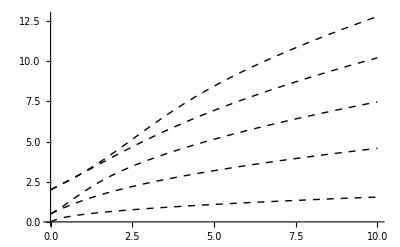

```mathematica
(* Plotting the exact values *)
exactPlot = Plot[Take[Sort[Eigenvalues[linkH[h,100]//N]],5],{h,0,10},PlotStyle->{Black,Dashed,Thick}]
```

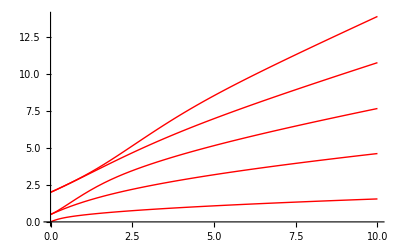

```mathematica
(* Plotting values given by our solution *)
linkPlot = Plot[Take[Sort[Eigenvalues[linkH[h,4]//N]],5],{h,0,10},PlotStyle->{Red,Thick}]
```

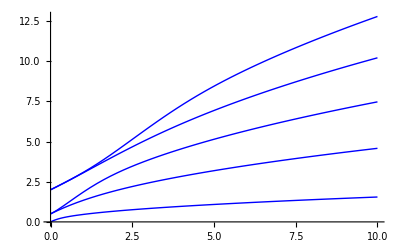

```mathematica
(* Plotting values given by our solution *)
linkPlot7 = Plot[Take[Sort[Eigenvalues[linkH[h,7]//N]],5],{h,0,10},PlotStyle->{Blue,Thick}]
```

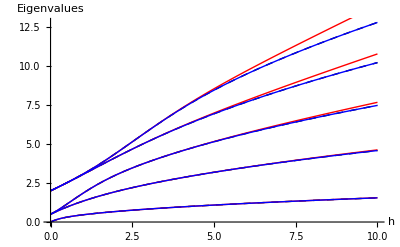

```mathematica
(* Looking at the difference between the two: as expected it works best when the gauge coupling constant is low *)
Show[exactPlot,linkPlot, linkPlot7, AxesLabel->{"h", "Eigenvalues"}]
```